```mathematica
(*Start more fancy method???*)
r0={1,0};
r1={0,1};
Lx=16;
Ly=16;
J=1;
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*non-periodic*)
Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dy,0,0}],{i,1,Length[Bonds]}];
(*Kugelkoordinaten*)
S[ϕ_,θ_]:={Cos[ϕ]Sin[θ],Sin[ϕ]Sin[θ],Cos[θ]};
Neelstatearglist=Flatten[{Table[{ϕlist⟦i⟧,0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧,(1-(-1)^i)*π/2},{i,1,Lx*Ly}]},1];
```

```mathematica
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
```

```mathematica
tingeldangelbob=Module[{dd,step=0.01,dangle={},MinArgList=Neelstatearglist},
For[dd=0.00,dd≤0.2,dd=dd+step,
(*MinArgList=FindMinimum[{Hnew/.{dx->dd,dy->dd+step},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;*)
MinArgList=FindMinimum[{Hnew/.{dx->dd,dy->dd},And@@Flatten[{Table[ϕlist⟦i⟧>-π && ϕlist⟦i⟧≤π,{i,Length[ϕlist]}],Table[θlist⟦i⟧>0 && θlist⟦i⟧≤π,{i,Length[θlist]}]}]},MinArgList]⟦2⟧/.Rule->List;
(*MinArgList=FindMinimum[Hnew/.{dx->dd+step,dy->dd},MinArgList,Method->"PrincipalAxis"]⟦2⟧/.Rule->List;
MinArgList=FindMinimum[Hnew/.{dx->dd+step,dy->dd+step},MinArgList,Method->"PrincipalAxis"]⟦2⟧/.Rule->List;*)
AppendTo[dangle,Flatten[{dd,Transpose[MinArgList][[2]]}]];
];
dangle
];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

```mathematica
θarray=ArrayReshape[tingeldangelbob[[-1,Lx*Ly+2;;-1]],{Ly,Lx}];
ϕarray=ArrayReshape[tingeldangelbob[[-1,2;;Lx*Ly+1]],{Ly,Lx}];
Grid[{{ArrayPlot[ϕarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[θarray,PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],ArrayPlot[Chop[Differences[ϕarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"],,ArrayPlot[Chop[Differences[θarray]],PlotLegends->Automatic,Mesh->True,ColorFunction->"Rainbow"]}}]
```

-Graphics- | -Graphics- | -Graphics- |  | -Graphics-

```mathematica
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,0,Ly-1}]}];
```

```mathematica
textureplot[tingeldangelbob[[-1,2;;]]]
```

-Graphics3D-

```mathematica
n=0;
Table[l[[y*Lx+1+n]],{y,0,Ly-1}]
Table[l[[n*Ly+x]],{x,1,Lx}]
```

{{0,0},{0,1},{0,2},{0,3}}

{{0,0},{1,0},{2,0},{3,0}}

```mathematica
Table[l[[(y)*Lx+1+x]],{y,0,Ly-1},{x,0,Lx-1}]
```

{{{0,0},{1,0},{2,0},{3,0}},{{0,1},{1,1},{2,1},{3,1}},{{0,2},{1,2},{2,2},{3,2}},{{0,3},{1,3},{2,3},{3,3}}}

```mathematica
ϕplotlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θplotlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
(*ϕplotlist=Neelstatearglist[[1;;Lx*Ly,2]];
θplotlist=Neelstatearglist[[Lx*Ly+1;;2*Lx*Ly,2]];*)
help=Table[Flatten[Table[{{0.2,0,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧]]},{y,0,Ly-2}]],{x,0,Lx-1}];
testlisty=Table[Flatten[Table[{help[[i]][[j]],0},{i,1,Ly-1}]],{j,1,Lx-1}];
testlistx=Table[Flatten[Table[{0,{0,-0.2,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+x+2⟧,θplotlist⟦(y)*Lx+x+2⟧]]},{x,0,Lx-2}]],{y,0,Ly-1}];
testlist3=Table[{testlistx[[i]],testlisty[[i]]},{i,1,Length[testlistx]-1}];
MatrixPlot[testlistx,PlotLegends->Automatic]
MatrixPlot[testlisty,PlotLegends->Automatic]
MatrixPlot[Flatten[testlist3,1],PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Clear[bklist]
bklist[κ_]:=Flatten[{dx->tingeldangelbob[[κ,1]],Table[Flatten[{ϕlist,θlist}]⟦i⟧->tingeldangelbob[[κ,2;;]]⟦i⟧,{i,1,2Lx*Ly}]}];
dy=0.2;
xspiralstate=Flatten[{{dx->0.2},Table[{ϕlist⟦i⟧->0},{i,1,Lx*Ly}],
Table[{θlist⟦i⟧->l⟦i⟧⟦1⟧*ArcTan[dy]+0*l⟦i⟧⟦2⟧*ArcTan[dy]},{i,1,Lx*Ly}]}];
```

```mathematica
Hnew/.xspiralstate
```

23.2963

```mathematica
Hnew/.bklist[-1]
Hnew/.bklist[1]
```

-485.726

-384.

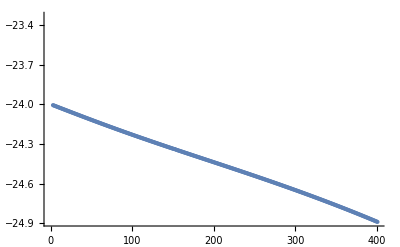

```mathematica
ListPlot[Table[Hnew/.bklist[s],{s,1,Length[tingeldangelbob]}]]
```

```mathematica
Hnew/.bklist[Length[tingeldangelbob]]
```

Cos[θ1000] Cos[θ1001]+Cos[θ1001] Cos[θ1002]+Cos[θ1002] Cos[θ1003]+Cos[θ1003] Cos[θ1004]+Cos[θ1004] Cos[θ1005]+Cos[θ1005] Cos[θ1006]+Cos[θ1006] Cos[θ1007]+Cos[θ1007] Cos[θ1008]+Cos[θ1008] Cos[θ1009]+Cos[θ100] Cos[θ101]+8940+Sin[θ996] Sin[θ997] Sin[ϕ996] Sin[ϕ997]+0.2 (Cos[θ997] Sin[θ965] Sin[ϕ965]-Cos[θ965] Sin[θ997] Sin[ϕ997])+Sin[θ966] Sin[θ998] Sin[ϕ966] Sin[ϕ998]+Sin[θ997] Sin[θ998] Sin[ϕ997] Sin[ϕ998]+0.2 (Cos[θ998] Sin[θ966] Sin[ϕ966]-Cos[θ966] Sin[θ998] Sin[ϕ998])+Sin[θ1000] Sin[θ999] Sin[ϕ1000] Sin[ϕ999]+Sin[θ967] Sin[θ999] Sin[ϕ967] Sin[ϕ999]+Sin[θ998] Sin[θ999] Sin[ϕ998] Sin[ϕ999]+0.2 (Cos[θ999] Sin[θ967] Sin[ϕ967]-Cos[θ967] Sin[θ999] Sin[ϕ999])
 |  |  |  |

```mathematica
energydimlist={{6,6,-61.05555394924338},{4,4,-24.4402717784584},{8,8,-113.73689770841767},{10,10,-182.38882635505993},{12,12,-267.3598190692088},{14,14,-368.5767116763112},{16,16,-485.72632301175025},{18,18,-619.025472659022},{20,20,-769.0483143590886},{22,22,-934.760300729925},{24,24,-1116.5111266724389},{32,32,-2003.612660646481}};
```

```mathematica
bklist[κ_]:=Flatten[{dx->tingeldangelbob[[κ,1]],Table[Flatten[{ϕlist,θlist}]⟦i⟧->tingeldangelbob[[κ,2;;]]⟦i⟧,{i,1,2Lx*Ly}]}];
AppendTo[energydimlist,{Lx,Ly,(Hnew/.bklist[Length[tingeldangelbob]])}]
```

{{6,6,-61.0556},{4,4,-24.4403},{8,8,-113.737},{10,10,-182.389},{12,12,-267.36},{14,14,-368.577},{16,16,-485.726},{18,18,-619.025},{20,20,-769.048},{22,22,-934.76},{24,24,-1116.51},{32,32,-2003.61}}

```mathematica
(*spin chirality*)
x=0;
y=0;
ϕplotlist=tingeldangelbob⟦-1,2;;Lx*Ly+1⟧;
θplotlist=tingeldangelbob⟦-1,Lx*Ly+2;;2Lx*Ly+1⟧;
chirallist=Table[S[ϕplotlist⟦(y)*Lx+1+x⟧,θplotlist⟦(y)*Lx+1+x⟧].Cross[S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+1+x+1⟧,θplotlist⟦(y)*Lx+1+x+1⟧]],{x,0,Lx-2},{y,0,Ly-2}];
```

```mathematica
MatrixPlot[chirallist,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Sum[chirallist[[i]][[j]],{i,1,Lx-1},{j,1,Ly-1}]
Sum[(-1)^(i+j)*chirallist[[i]][[j]],{i,1,Lx-1},{j,1,Ly-1}]
```

0.12193

-0.472838

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bkoehler/Documents/Wolfram Mathematica/Dzyaloshinskii_Moriya

```mathematica
plist
```

```mathematica
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
alist=Flatten[{plist,tlist}];
```

Import::nffil: File Angleplot/xsize17ysize17fieldsize17/phiplotD50cJ.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File Angleplot/xsize17ysize17fieldsize17/thetaplotD50cJ.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
Lx=16;
Ly=16;
textureplot[arglist_]:=Graphics3D[{PointSize[0.01],Point[Flatten[Table[Table[{i,j,0},{i,0,Lx-1}],{j,0,Lx-1}],1]],Table[Arrow[Tube[{{i,j,0},{i,j,0}+1*S[arglist[[i*Ly+j+1]],arglist[[i*Ly+j+1+Lx*Ly]]]}]],{i,0,Lx-1},{j,0,Ly-1}]}];
d=50;
Manipulate[
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
alist=Flatten[{plist,tlist}];
textureplot[Flatten[alist]]
,{d,0,100,1}]
```

Import::nffil: File Angleplot/xsize16ysize16fieldsize16/phiplotD31cJ.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File Angleplot/xsize16ysize16fieldsize16/thetaplotD31cJ.dat not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

```mathematica
spiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-l⟦i⟧⟦1⟧*ArcTan[dx]-0*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
BKListspiral=Flatten[{Table[0,{i,1,Length[ϕlist]}],Table[spiraltlist⟦i⟧,{i,Length[θlist]}]}];
```

```mathematica
textureplot[BKListspiral]
```

-Graphics3D-

```mathematica
Hnew/.bklist[Length[tingeldangelbob]]
```

```mathematica
l[[Lx]]
```

{15,0}

```mathematica
BulkBonds=DeleteCases[Flatten[Table[If[i<j&&l[[i,1]]!=0&&l[[i,2]]!=0&&l[[i,1]]≠Lx-1&&l[[i,2]]≠Ly-1&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
```

{{18,19},{18,34},{19,20},{19,35},{20,21},{20,36},{21,22},{21,37},{22,23},{22,38},{23,24},{23,39},{24,25},{24,40},{25,26},{25,41},{26,27},{26,42},{27,28},{27,43},{28,29},{28,44},{29,30},{29,45},{30,31},{30,46},{31,32},{31,47},{34,35},{34,50},{35,36},{35,51},{36,37},{36,52},{37,38},{37,53},{38,39},{38,54},{39,40},{39,55},{40,41},{40,56},{41,42},{41,57},{42,43},{42,58},{43,44},{43,59},{44,45},{44,60},{45,46},{45,61},{46,47},{46,62},{47,48},{47,63},{50,51},{50,66},{51,52},{51,67},{52,53},{52,68},{53,54},{53,69},{54,55},{54,70},{55,56},{55,71},{56,57},{56,72},{57,58},{57,73},{58,59},{58,74},{59,60},{59,75},{60,61},{60,76},{61,62},{61,77},{62,63},{62,78},{63,64},{63,79},{66,67},{66,82},{67,68},{67,83},{68,69},{68,84},{69,70},{69,85},{70,71},{70,86},{71,72},{71,87},{72,73},{72,88},{73,74},{73,89},{74,75},{74,90},{75,76},{75,91},{76,77},{76,92},{77,78},{77,93},{78,79},{78,94},{79,80},{79,95},{82,83},{82,98},{83,84},{83,99},{84,85},{84,100},{85,86},{85,101},{86,87},{86,102},{87,88},{87,103},{88,89},{88,104},{89,90},{89,105},{90,91},{90,106},{91,92},{91,107},{92,93},{92,108},{93,94},{93,109},{94,95},{94,110},{95,96},{95,111},{98,99},{98,114},{99,100},{99,115},{100,101},{100,116},{101,102},{101,117},{102,103},{102,118},{103,104},{103,119},{104,105},{104,120},{105,106},{105,121},{106,107},{106,122},{107,108},{107,123},{108,109},{108,124},{109,110},{109,125},{110,111},{110,126},{111,112},{111,127},{114,115},{114,130},{115,116},{115,131},{116,117},{116,132},{117,118},{117,133},{118,119},{118,134},{119,120},{119,135},{120,121},{120,136},{121,122},{121,137},{122,123},{122,138},{123,124},{123,139},{124,125},{124,140},{125,126},{125,141},{126,127},{126,142},{127,128},{127,143},{130,131},{130,146},{131,132},{131,147},{132,133},{132,148},{133,134},{133,149},{134,135},{134,150},{135,136},{135,151},{136,137},{136,152},{137,138},{137,153},{138,139},{138,154},{139,140},{139,155},{140,141},{140,156},{141,142},{141,157},{142,143},{142,158},{143,144},{143,159},{146,147},{146,162},{147,148},{147,163},{148,149},{148,164},{149,150},{149,165},{150,151},{150,166},{151,152},{151,167},{152,153},{152,168},{153,154},{153,169},{154,155},{154,170},{155,156},{155,171},{156,157},{156,172},{157,158},{157,173},{158,159},{158,174},{159,160},{159,175},{162,163},{162,178},{163,164},{163,179},{164,165},{164,180},{165,166},{165,181},{166,167},{166,182},{167,168},{167,183},{168,169},{168,184},{169,170},{169,185},{170,171},{170,186},{171,172},{171,187},{172,173},{172,188},{173,174},{173,189},{174,175},{174,190},{175,176},{175,191},{178,179},{178,194},{179,180},{179,195},{180,181},{180,196},{181,182},{181,197},{182,183},{182,198},{183,184},{183,199},{184,185},{184,200},{185,186},{185,201},{186,187},{186,202},{187,188},{187,203},{188,189},{188,204},{189,190},{189,205},{190,191},{190,206},{191,192},{191,207},{194,195},{194,210},{195,196},{195,211},{196,197},{196,212},{197,198},{197,213},{198,199},{198,214},{199,200},{199,215},{200,201},{200,216},{201,202},{201,217},{202,203},{202,218},{203,204},{203,219},{204,205},{204,220},{205,206},{205,221},{206,207},{206,222},{207,208},{207,223},{210,211},{210,226},{211,212},{211,227},{212,213},{212,228},{213,214},{213,229},{214,215},{214,230},{215,216},{215,231},{216,217},{216,232},{217,218},{217,233},{218,219},{218,234},{219,220},{219,235},{220,221},{220,236},{221,222},{221,237},{222,223},{222,238},{223,224},{223,239},{226,227},{226,242},{227,228},{227,243},{228,229},{228,244},{229,230},{229,245},{230,231},{230,246},{231,232},{231,247},{232,233},{232,248},{233,234},{233,249},{234,235},{234,250},{235,236},{235,251},{236,237},{236,252},{237,238},{237,253},{238,239},{238,254},{239,240},{239,255}}

```mathematica
Lx=32;
Ly=8;
d=20;
dx=d/100;
ϕlist=Flatten[Table[{ToExpression["ϕ"<>ToString[i]]},{i,1,Lx*Ly}]];
θlist=Flatten[Table[{ToExpression["θ"<>ToString[i]]},{i,1,Lx*Ly}]];
l=Flatten[Table[x*r0+y*r1,{y,0,Ly-1},{x,0,Lx-1}],1];
(*Bonds=DeleteCases[Flatten[Table[If[i<j&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];*)
border=0;
BulkBonds=DeleteCases[Flatten[Table[If[i<j&&l[[i,1]]≥border&&l[[i,2]]>=border&&l[[i,1]]<Lx-border&&l[[i,2]]<Ly-border&&Norm[l[[i]]-l[[j]]]==1,{i,j},"a"],{i,1,Length[l]},{j,1,Length[l]}],1],_String];
Bonds=BulkBonds;
dBonds=Table[If[(l⟦Bonds⟦i,2⟧⟧-l⟦Bonds⟦i,1⟧⟧)⟦1⟧≠0&&l⟦Bonds⟦i,1⟧⟧⟦1⟧≥0,{ 0,-dx,0},{dx,0,0}],{i,1,Length[Bonds]}];
Hnew=Sum[J*(S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧].S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧])+
dBonds⟦i⟧.(Cross[S[ϕlist⟦Bonds⟦i,1⟧⟧,θlist⟦Bonds⟦i,1⟧⟧],S[ϕlist⟦Bonds⟦i,2⟧⟧,θlist⟦Bonds⟦i,2⟧⟧]]),{i,1,Length[Bonds]}];
```

```mathematica
plist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/phiplotD"<>ToString[d]<>"cJ.dat","Table"]];
tlist=Flatten[Import["Angleplot/xsize"<>ToString[Lx]<>"ysize"<>ToString[Ly]<>"fieldsize"<>ToString[Lx]<>"/thetaplotD"<>ToString[d]<>"cJ.dat","Table"]];
BKList=Table[Flatten[{ϕlist,θlist}]⟦i⟧->Flatten[{plist,tlist}][[i]],{i,Length[ϕlist]+Length[θlist]}];
spiraltlist=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2-0*l⟦i⟧⟦1⟧*ArcTan[dx]+l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
BKListspiral=Flatten[{Table[ϕlist⟦i⟧->-π/2,{i,1,Length[ϕlist]}],Table[θlist⟦i⟧->spiraltlist⟦i⟧,{i,Length[θlist]}]}];
Neelstatearglist=Flatten[{Table[ϕlist⟦i⟧->0,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧))*π/2,{i,1,Lx*Ly}]},1];
```

```mathematica
N[Hnew/.Neelstatearglist]
N[Hnew/.BKList]
N[Hnew/.BKListspiral]
```

-472.

-458.572

-476.436

```mathematica
Modulo[y_]:=Module[{x=Mod[y,2π]},
If[x>π,2π-x,x]
];
spiraltlist=Table[Modulo[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧+1))*π/2-1*l⟦i⟧⟦1⟧*ArcTan[dx]+0*l⟦i⟧⟦2⟧*ArcTan[dx]],{i,1,Lx*Ly}];
spiraltlistdumb=Table[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧+1))*π/2-1*l⟦i⟧⟦1⟧*ArcTan[dx]+0*l⟦i⟧⟦2⟧*ArcTan[dx],{i,1,Lx*Ly}];
BKListspiral=Flatten[{Table[ϕlist⟦i⟧->-π/2,{i,1,Length[ϕlist]}],Table[θlist⟦i⟧->spiraltlistdumb⟦i⟧,{i,Length[θlist]}]}];
Neelstatearglist=Flatten[{Table[ϕlist⟦i⟧->0,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->Mod[(l[[i]][[1]]-l[[i]][[2]]),2],{i,1,Lx*Ly}]},1];
Randarglist=Flatten[{Table[ϕlist⟦i⟧->RandomReal[]*2π,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->RandomReal[]*π,{i,1,Lx*Ly}]},1];
Randarglist22=Flatten[{Table[ϕlist⟦i⟧->1,{i,1,Lx*Ly}],
Table[θlist⟦i⟧->1+π/2,{i,1,Lx*Ly}]},1];
GradNik=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.BKListspiral;
GradNeel=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.Neelstatearglist;
GradRand=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.Randarglist;
GradRand17=N@D[Hnew,{Flatten[{ϕlist,θlist}]}]/.Randarglist22;
```

```mathematica
Neelstatearglist
```

{ϕ1→0,ϕ2→0,ϕ3→0,ϕ4→0,ϕ5→0,ϕ6→0,ϕ7→0,ϕ8→0,ϕ9→0,ϕ10→0,ϕ11→0,ϕ12→0,ϕ13→0,ϕ14→0,ϕ15→0,ϕ16→0,ϕ17→0,ϕ18→0,ϕ19→0,ϕ20→0,ϕ21→0,ϕ22→0,ϕ23→0,ϕ24→0,ϕ25→0,ϕ26→0,ϕ27→0,ϕ28→0,ϕ29→0,ϕ30→0,ϕ31→0,ϕ32→0,ϕ33→0,ϕ34→0,ϕ35→0,ϕ36→0,ϕ37→0,ϕ38→0,ϕ39→0,ϕ40→0,ϕ41→0,ϕ42→0,ϕ43→0,ϕ44→0,ϕ45→0,ϕ46→0,ϕ47→0,ϕ48→0,ϕ49→0,ϕ50→0,ϕ51→0,ϕ52→0,ϕ53→0,ϕ54→0,ϕ55→0,ϕ56→0,ϕ57→0,ϕ58→0,ϕ59→0,ϕ60→0,ϕ61→0,ϕ62→0,ϕ63→0,ϕ64→0,ϕ65→0,ϕ66→0,ϕ67→0,ϕ68→0,ϕ69→0,ϕ70→0,ϕ71→0,ϕ72→0,ϕ73→0,ϕ74→0,ϕ75→0,ϕ76→0,ϕ77→0,ϕ78→0,ϕ79→0,ϕ80→0,ϕ81→0,ϕ82→0,ϕ83→0,ϕ84→0,ϕ85→0,ϕ86→0,ϕ87→0,ϕ88→0,ϕ89→0,ϕ90→0,ϕ91→0,ϕ92→0,ϕ93→0,ϕ94→0,ϕ95→0,ϕ96→0,ϕ97→0,ϕ98→0,ϕ99→0,ϕ100→0,ϕ101→0,ϕ102→0,ϕ103→0,ϕ104→0,ϕ105→0,ϕ106→0,ϕ107→0,ϕ108→0,ϕ109→0,ϕ110→0,ϕ111→0,ϕ112→0,ϕ113→0,ϕ114→0,ϕ115→0,ϕ116→0,ϕ117→0,ϕ118→0,ϕ119→0,ϕ120→0,ϕ121→0,ϕ122→0,ϕ123→0,ϕ124→0,ϕ125→0,ϕ126→0,ϕ127→0,ϕ128→0,ϕ129→0,ϕ130→0,ϕ131→0,ϕ132→0,ϕ133→0,ϕ134→0,ϕ135→0,ϕ136→0,ϕ137→0,ϕ138→0,ϕ139→0,ϕ140→0,ϕ141→0,ϕ142→0,ϕ143→0,ϕ144→0,ϕ145→0,ϕ146→0,ϕ147→0,ϕ148→0,ϕ149→0,ϕ150→0,ϕ151→0,ϕ152→0,ϕ153→0,ϕ154→0,ϕ155→0,ϕ156→0,ϕ157→0,ϕ158→0,ϕ159→0,ϕ160→0,ϕ161→0,ϕ162→0,ϕ163→0,ϕ164→0,ϕ165→0,ϕ166→0,ϕ167→0,ϕ168→0,ϕ169→0,ϕ170→0,ϕ171→0,ϕ172→0,ϕ173→0,ϕ174→0,ϕ175→0,ϕ176→0,ϕ177→0,ϕ178→0,ϕ179→0,ϕ180→0,ϕ181→0,ϕ182→0,ϕ183→0,ϕ184→0,ϕ185→0,ϕ186→0,ϕ187→0,ϕ188→0,ϕ189→0,ϕ190→0,ϕ191→0,ϕ192→0,ϕ193→0,ϕ194→0,ϕ195→0,ϕ196→0,ϕ197→0,ϕ198→0,ϕ199→0,ϕ200→0,ϕ201→0,ϕ202→0,ϕ203→0,ϕ204→0,ϕ205→0,ϕ206→0,ϕ207→0,ϕ208→0,ϕ209→0,ϕ210→0,ϕ211→0,ϕ212→0,ϕ213→0,ϕ214→0,ϕ215→0,ϕ216→0,ϕ217→0,ϕ218→0,ϕ219→0,ϕ220→0,ϕ221→0,ϕ222→0,ϕ223→0,ϕ224→0,ϕ225→0,ϕ226→0,ϕ227→0,ϕ228→0,ϕ229→0,ϕ230→0,ϕ231→0,ϕ232→0,ϕ233→0,ϕ234→0,ϕ235→0,ϕ236→0,ϕ237→0,ϕ238→0,ϕ239→0,ϕ240→0,ϕ241→0,ϕ242→0,ϕ243→0,ϕ244→0,ϕ245→0,ϕ246→0,ϕ247→0,ϕ248→0,ϕ249→0,ϕ250→0,ϕ251→0,ϕ252→0,ϕ253→0,ϕ254→0,ϕ255→0,ϕ256→0,θ1→0,θ2→1,θ3→0,θ4→1,θ5→0,θ6→1,θ7→0,θ8→1,θ9→0,θ10→1,θ11→0,θ12→1,θ13→0,θ14→1,θ15→0,θ16→1,θ17→1,θ18→0,θ19→1,θ20→0,θ21→1,θ22→0,θ23→1,θ24→0,θ25→1,θ26→0,θ27→1,θ28→0,θ29→1,θ30→0,θ31→1,θ32→0,θ33→0,θ34→1,θ35→0,θ36→1,θ37→0,θ38→1,θ39→0,θ40→1,θ41→0,θ42→1,θ43→0,θ44→1,θ45→0,θ46→1,θ47→0,θ48→1,θ49→1,θ50→0,θ51→1,θ52→0,θ53→1,θ54→0,θ55→1,θ56→0,θ57→1,θ58→0,θ59→1,θ60→0,θ61→1,θ62→0,θ63→1,θ64→0,θ65→0,θ66→1,θ67→0,θ68→1,θ69→0,θ70→1,θ71→0,θ72→1,θ73→0,θ74→1,θ75→0,θ76→1,θ77→0,θ78→1,θ79→0,θ80→1,θ81→1,θ82→0,θ83→1,θ84→0,θ85→1,θ86→0,θ87→1,θ88→0,θ89→1,θ90→0,θ91→1,θ92→0,θ93→1,θ94→0,θ95→1,θ96→0,θ97→0,θ98→1,θ99→0,θ100→1,θ101→0,θ102→1,θ103→0,θ104→1,θ105→0,θ106→1,θ107→0,θ108→1,θ109→0,θ110→1,θ111→0,θ112→1,θ113→1,θ114→0,θ115→1,θ116→0,θ117→1,θ118→0,θ119→1,θ120→0,θ121→1,θ122→0,θ123→1,θ124→0,θ125→1,θ126→0,θ127→1,θ128→0,θ129→0,θ130→1,θ131→0,θ132→1,θ133→0,θ134→1,θ135→0,θ136→1,θ137→0,θ138→1,θ139→0,θ140→1,θ141→0,θ142→1,θ143→0,θ144→1,θ145→1,θ146→0,θ147→1,θ148→0,θ149→1,θ150→0,θ151→1,θ152→0,θ153→1,θ154→0,θ155→1,θ156→0,θ157→1,θ158→0,θ159→1,θ160→0,θ161→0,θ162→1,θ163→0,θ164→1,θ165→0,θ166→1,θ167→0,θ168→1,θ169→0,θ170→1,θ171→0,θ172→1,θ173→0,θ174→1,θ175→0,θ176→1,θ177→1,θ178→0,θ179→1,θ180→0,θ181→1,θ182→0,θ183→1,θ184→0,θ185→1,θ186→0,θ187→1,θ188→0,θ189→1,θ190→0,θ191→1,θ192→0,θ193→0,θ194→1,θ195→0,θ196→1,θ197→0,θ198→1,θ199→0,θ200→1,θ201→0,θ202→1,θ203→0,θ204→1,θ205→0,θ206→1,θ207→0,θ208→1,θ209→1,θ210→0,θ211→1,θ212→0,θ213→1,θ214→0,θ215→1,θ216→0,θ217→1,θ218→0,θ219→1,θ220→0,θ221→1,θ222→0,θ223→1,θ224→0,θ225→0,θ226→1,θ227→0,θ228→1,θ229→0,θ230→1,θ231→0,θ232→1,θ233→0,θ234→1,θ235→0,θ236→1,θ237→0,θ238→1,θ239→0,θ240→1,θ241→1,θ242→0,θ243→1,θ244→0,θ245→1,θ246→0,θ247→1,θ248→0,θ249→1,θ250→0,θ251→1,θ252→0,θ253→1,θ254→0,θ255→1,θ256→0}

```mathematica
MatrixPlot[ArrayReshape[GradRand[[Lx*Ly+1;;-1]],{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Chop[ArrayReshape[GradRand17[[Lx*Ly+1;;-1]],{Lx,Ly}]]
```

{{0.276355,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.168294,0.0602337},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{0.10806,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-0.10806},{-0.0602337,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.168294,-0.276355}}

```mathematica
MatrixForm[%]
```

(0.276355 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.168294 | 0.0602337
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
0.10806 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.10806
-0.0602337 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.168294 | -0.276355)

```mathematica
MatrixPlot[ArrayReshape[GradRand17[[Lx*Ly+1;;-1]],{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
MatrixPlot[Chop[ArrayReshape[GradNeel[[Lx*Ly+1;;-1]],{Lx,Ly}]],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Cross[{xx,yy,0},{0,0,1}]
Cross[{yy,-xx,0},{0,0,1}]
```

{yy,-xx,0}

{-xx,-yy,0}

```mathematica
({{Cos[π/2], Sin[π/2]}, {-Sin[π/2], Cos[π/2]}}).{xx,yy}
```

{yy,-xx}

```mathematica
-(Sin[yy+xx]-Cos[yy+xx])/.xx->π/2
Cos[yy+xx]+Sin[yy+xx]/.xx->π/2
```

-Cos[yy]-Sin[yy]

Cos[yy]-Sin[yy]

```mathematica
ArrayReshape[GradNeel[[Lx*Ly+1;;-1]],{Lx,Ly}]//MatrixForm
```

(1.791 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -1.791
-2.41635 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 2.41635
2.63247 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -2.63247
-2.41635 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 2.41635
2.63247 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -2.63247
-2.41635 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 2.41635
2.63247 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -2.63247
-2.41635 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 2.41635
2.63247 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -2.63247
-2.41635 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 2.41635
2.63247 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -2.63247
-2.41635 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 2.41635
2.63247 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -2.63247
-2.41635 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 2.41635
2.63247 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -3.36588 | 3.36588 | -2.63247
-1.57488 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 2.52441 | -2.52441 | 1.57488)

```mathematica
MatrixPlot[ArrayReshape[GradNik[[Lx*Ly+1;;-1]],{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
ArrayReshape[GradNik[[Lx*Ly+1;;-1]],{Lx,Ly}]//MatrixForm
```

(0.396116 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.2 | 0.00388386
0.196116 | -5.55112×10^-17 | 2.22045×10^-16 | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 3.60822×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 3.60822×10^-16 | -4.51028×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 2.22045×10^-16 | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 3.60822×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 3.05311×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 2.22045×10^-16 | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
0.196116 | -5.55112×10^-17 | 0. | 0. | 2.22045×10^-16 | 1.11022×10^-16 | -4.996×10^-16 | 2.498×10^-16 | -3.81639×10^-17 | -2.22045×10^-16 | -1.11022×10^-16 | 1.66533×10^-16 | 2.22045×10^-16 | -4.996×10^-16 | 5.27356×10^-16 | -0.196116
-0.00388386 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.2 | -0.396116)

```mathematica
-24.4402717784584
```

```mathematica
MatrixPlot[ArrayReshape[tlist-spiraltlist,{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
Modulo[y_]:=Module[{x=Mod[y,2π]},
If[x>π,2π-x,x]
];
```

```mathematica
spiraltlist=Table[Modulo[(1-(-1)^(l⟦i⟧⟦1⟧+l⟦i⟧⟦2⟧+1))*π/2-0*l⟦i⟧⟦1⟧*ArcTan[dx]+l⟦i⟧⟦2⟧*ArcTan[dx]],{i,1,Lx*Ly}];
(*MatrixPlot[ArrayReshape[Table[-π/2,{i,1,Length[ϕlist]}],{Lx,Ly}],PlotLegends->Automatic]*)
MatrixPlot[ArrayReshape[spiraltlist,{Lx,Ly}],PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*MatrixPlot[ArrayReshape[plist,{Lx,Ly}],PlotLegends->Automatic]*)
MatrixPlot[ArrayReshape[tlist,{Lx,Ly}],PlotLegends->Automatic,PlotRange->{0,π}]
```

-Graphics-

```mathematica
dBonds
```

{{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},{0,-2/5,0},{2/5,0,0},1916,{0,-2/5,0},{2/5,0,0},{2/5,0,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0},{0,-2/5,0}}
 |  |  |  |

```mathematica
ϕplotlist=plist;
θplotlist=tlist;
(*ϕplotlist=Neelstatearglist[[1;;Lx*Ly,2]];
θplotlist=Neelstatearglist[[Lx*Ly+1;;2*Lx*Ly,2]];*)
help=Table[Flatten[Table[{{0.2,0,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y+1)*Lx+1+x⟧,θplotlist⟦(y+1)*Lx+1+x⟧]]},{y,0,Ly-2}]],{x,0,Lx-1}];
testlisty=Table[Flatten[Table[{help[[i]][[j]],0},{i,1,Ly-1}]],{j,1,Lx-1}];
testlistx=Table[Flatten[Table[{0,{0,-0.2,0}.Cross[S[ϕplotlist⟦y*Lx+1+x⟧,θplotlist⟦y*Lx+1+x⟧],S[ϕplotlist⟦(y)*Lx+x+2⟧,θplotlist⟦(y)*Lx+x+2⟧]]},{x,0,Lx-2}]],{y,0,Ly-1}];
testlist3=Table[{testlistx[[i]],testlisty[[i]]},{i,1,Length[testlistx]-1}];
MatrixPlot[testlistx,PlotLegends->Automatic]
MatrixPlot[testlisty,PlotLegends->Automatic]
MatrixPlot[Flatten[testlist3,1],PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-